# Physics 230 -- Lab 14 (Sample Final Exam)

A two-hour closed-book/notes in-class final exam will be administered during the regularly-scheduled final exam period.  It will consist of a Mathematica notebook file containing six exam problems.  Your instructor and/or TA can clarify the meaning of the problem descriptions, but will not answer any other questions.  The only external resource that you are permitted to access is the built-in Mathematica Documentation Center.  Partial credit will be considered for problems that are only partially complete at the end of the exam period.

We provide a few sample exam problems here so that you will have some idea of what to expect on the actual exam.  A new version of this lab containing solutions will be posted during reading days.

## (#1)

```mathematica
Tooltip
```

Plot the expression,  ⅇ^(-x^2), and its first four derivatives, all on the same graph over the range {x, -2, 2}.  Make sure that none of the curves get cut off at the top or bottom.

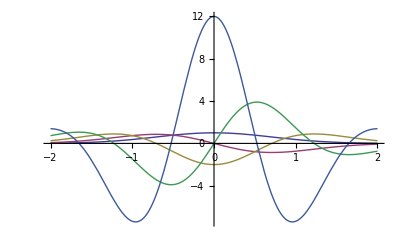

```mathematica
eq = Exp[-x^2];
eqs = Table[Tooltip[D[eq,{x,i}]],{i,0,4}];
Plot[{eqs},{x,-2,2},PlotRange->All]
```

## (#2)

Calculate the x = 0 Taylor-series expansion of ⅇ^(-x^2)up to 9th order.  Plot this series approximation, together with the exact expression, on the same graph over the range {x, -2, 2}.

1-x^2+x^4/2-x^6/6+x^8/24

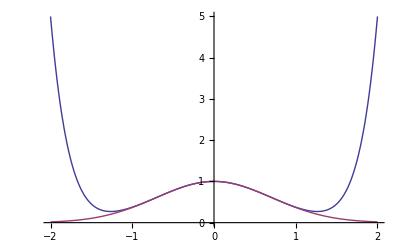

```mathematica
ser = Series[Exp[-x^2],{x,0,9}]//Normal
Plot[Tooltip[{ser,eq}],{x,-2,2},PlotRange->All]
```

## (#3)

Consider vectors A and B defined below.  Determine the sum, scalar product, and matrix direct product of A and B, the cross product of A and B, the magnitude of A, the direction (i.e. unit vector) of A, and the angle between A and B (displayed as a floating-point number in degrees).

```mathematica
A= {2,7,-3};
B= {-1,0,5};
(*what is the matrix direct product*)
A+B
A.B
KroneckerProduct[A,B]//MatrixForm
Cross[A,B]
Norm[A]
Normalize[A]
rad = N[VectorAngle[A,B]]Degree
```

{1,7,2}

-17

(-2 | 0 | 10
-7 | 0 | 35
3 | 0 | -15)

{35,-7,7}

√62

{√(2/31),7/(√62),-3/(√62)}

0.0350464

## (#4)

Find the value of x where x = ⅇ^(-x^2).

```mathematica
ans= x/.Solve[x==Exp[-x^2],x]//N
Exp[-ans[[1]]^2]==ans[[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{0.652919}

True

## (#5)

Find all of the minima and maxima of the function f=x^4-3 x^2 in the range -2<x<2, not including the endpoints of the range.  Start with a plot that will help you to visualize the results.  Use list extraction and variable-replacement techniques to return each result as a single number (not a list or a replacement rule).

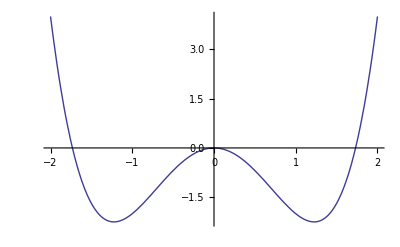

-√(3/2)

0

√(3/2)

```mathematica
fun5 = x^4-3 x^2;
Plot[fun5,{x,-2,2}]
answers = x/.Solve[D[fun5,x]==0,x];
min1 = answers[[2]]
max = answers[[1]]
min2 = answers[[3]]
```

## (#6)

Find all xy points that simultaneously satisfy the pair of equations, x^2+y^2=1 and x^2-y^2=1/2.  Also ContourPlot both implicit equations on the same graph to visually verify the solutions.

{{x→-(√3)/2,y→-1/2},{x→-(√3)/2,y→1/2},{x→(√3)/2,y→-1/2},{x→(√3)/2,y→1/2}}

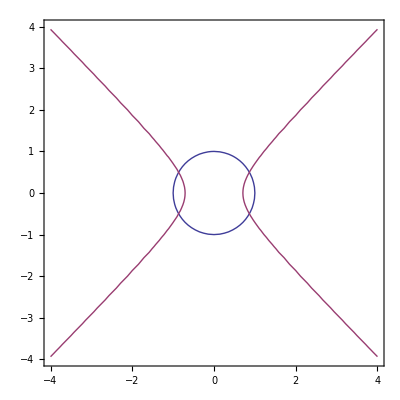

```mathematica
Solve[{x^2+y^2==1,x^2-y^2==1/2},{x,y}]
ContourPlot[{x^2+y^2==1,x^2-y^2==1/2},{x,-4,4},{y,-4,4},Axes->True,GridLines->{{-(√3)/2,(√3)/2},{-1/2,1/2}}](*checked!*)
```

## (#7)

Show that the Fourier transform of f = ⅇ^(-2(t-4)^2)-ⅇ^(-2(t+4)^2) is equal to  ⅈ ⅇ^(-1/8 ω^2)sin(4ω).  Plot f over the range {t, -8, 8}, and plot the imaginary part of its Fourier transform over the range {ω, -8, 8}.

ⅇ^(-2 (-4+t)^2)-ⅇ^(-2 (4+t)^2)

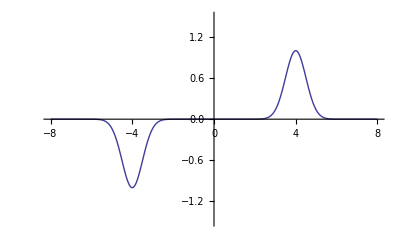

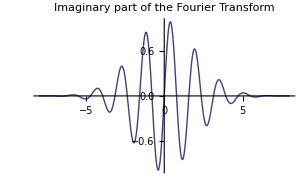
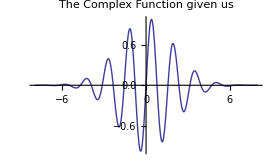

```mathematica
func7 = Exp[-2*(t-4)^2] - Exp[-2*(t+4)^2]
Plot[func7,{t,-8,8},PlotRange->{-1.5,1.5}]
fourier =FourierTransform[func7,t,w];
{Plot[Im[fourier],{w,-8,8},PlotLabel->"Imaginary part of the Fourier Transform"],Plot[Im[I*Exp[-1/8*w^2]*Sin[4*w]],{w,-8,8},PlotLabel->"The Complex Function given us"]}
```

## (#8)

The file airIndex.dat has two columns of numbers with the wavelength in μm in the first column and the second column is δn×10^8.  This is 10^8  times the difference between the index of refection of air and the index of refraction of a vacuum (which is exactly 1).  This data should be well fit by a function of the form δn×10^8=a+b/(c-1/λ^2)+d/(e-1/λ^2).  Find the constants a, b, c, d, and e which best fit this data (in the least squares sense) and the uncertainties in the fit parameters.  You should be able to fit each data point for the index to within 1.  The following ranges will give you a good starting point:
5000<a<15000, 1000000<b<3000000, 100<c<150, 10000 <d<50000, 10<e<60.

```mathematica
nlm8["BestFitParameters"]
```

{a→5000.02,b→2.09598×10^6,c→100.,d→10000.,e→10.7571}

```mathematica
Manipulate[Show[{ListPlot[data],Plot[(a+b/(c-1/λ^2)+d/(e-1/λ^2)),{λ,-2,3}]},PlotRange->{{0,2},{25000,30000}}],{{a,6480},5000,15000},{{b,2.18*^6},1000000,3000000},{{c,110},100,150},{{d,50000},10000,80000},{{e,54.2},10,80}]
```

{{0.2,32410.1},{0.21,31748.2},{0.22,31225.6},{0.23,30800.6},{0.24,30447.7},{0.25,30148.2},{0.26,29891.},{0.27,29670.3},{0.28,29477.2},{0.29,29305.9},{0.3,29157.8},{0.31,29022.6},{0.32,28904.},{0.33,28794.9},{0.34,28699.5},{0.35,28613.6},{0.36,28533.5},{0.37,28460.},{0.38,28393.9},{0.39,28332.1},{0.4,28277.6},{0.41,28223.5},{0.42,28178.3},{0.43,28132.7},{0.44,28089.1},{0.45,28053.8},{0.46,28017.9},{0.47,27985.6},{0.48,27953.4},{0.49,27925.8},{0.5,27896.3},{0.51,27872.1},{0.52,27847.7},{0.53,27824.6},{0.54,27804.5},{0.55,27783.4},{0.56,27765.4},{0.57,27747.8},{0.58,27726.6},{0.59,27713.7},{0.6,27697.4},{0.61,27683.9},{0.62,27669.2},{0.63,27656.},{0.64,27642.4},{0.65,27632.8},{0.66,27621.1},{0.67,27611.7},{0.68,27600.8},{0.69,27590.5},{0.7,27581.5},{0.71,27572.},{0.72,27563.2},{0.73,27554.6},{0.74,27549.},{0.75,27538.5},{0.76,27532.3},{0.77,27525.9},{0.78,27518.8},{0.79,27513.},{0.8,27505.8},{0.81,27500.},{0.82,27492.3},{0.83,27487.8},{0.84,27482.8},{0.85,27477.8},{0.86,27471.},{0.87,27466.9},{0.88,27463.7},{0.89,27456.7},{0.9,27452.8},{0.91,27447.7},{0.92,27444.5},{0.93,27442.1},{0.94,27436.3},{0.95,27432.9},{0.96,27430.3},{0.97,27428.3},{0.98,27423.8},{0.99,27421.2},{1.,27417.8},{1.05,27401.4},{1.1,27391.5},{1.15,27381.8},{1.2,27369.3},{1.25,27360.3},{1.3,27353.2},{1.35,27345.6},{1.4,27340.3},{1.45,27336.},{1.5,27330.1},{1.55,27327.8},{1.6,27323.},{1.65,27318.8},{1.7,27314.9},{1.75,27314.5},{1.8,27310.1},{1.85,27306.1},{1.9,27306.7},{1.95,27302.3},{2.,27302.1}}

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {4.86911×10^-7, 0.000639154, 6.21416×10^-8}, is returned.

FittedModel[7943.66+53289.7/(«18»-1/(«1»))+(2.33399×10^6)/(125.753-1/λ^2)]

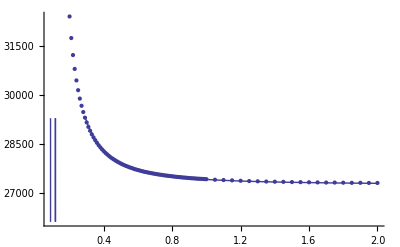

```mathematica
SetDirectory[NotebookDirectory[]];
data = Import["airIndex.dat"]
nlm8= NonlinearModelFit[data,{(a+b/(c-1/λ^2)+d/(e-1/λ^2)),6000<a<15000,2000000<b<3000000,109<c<150,30000<d<80000,50<e<100},{a,b,c,d,e},λ]
Show[{ListPlot[data],Plot[nlm8[x],{x,0,2}]},PlotRange->All]
```

```mathematica
first81 = Table[nlm8[i],{i,0.2,1,0.01}];
last20 = Table[nlm8[i],{i,1.05,2,0.05}];
total = Join[first81,last20]
δs = Transpose[data][[2]]
δs-total
Max[Abs[δs-total]] (*the first one is the furthest off*)
```

{32259.9,31682.5,31204.9,30804.3,30464.3,30173.,29921.1,29701.5,29508.9,29338.8,29187.9,29053.1,28932.3,28823.6,28725.3,28636.1,28555.,28480.9,28413.1,28350.9,28293.5,28240.7,28191.8,28146.5,28104.4,28065.3,28028.8,27994.8,27963.,27933.2,27905.2,27879.,27854.3,27831.1,27809.2,27788.5,27768.9,27750.4,27732.9,27716.3,27700.6,27685.6,27671.4,27657.9,27645.,27632.7,27621.,27609.9,27599.2,27589.,27579.3,27569.9,27561.,27552.4,27544.2,27536.3,27528.7,27521.5,27514.5,27507.8,27501.3,27495.1,27489.1,27483.3,27477.8,27472.4,27467.2,27462.2,27457.4,27452.7,27448.2,27443.9,27439.7,27435.6,27431.7,27427.8,27424.1,27420.6,27417.1,27413.7,27410.5,27395.5,27382.6,27371.3,27361.5,27352.8,27345.1,27338.2,27332.1,27326.5,27321.6,27317.1,27313.,27309.3,27305.9,27302.8,27300.,27297.4,27294.9,27292.7,27290.7}

{32410.1,31748.2,31225.6,30800.6,30447.7,30148.2,29891.,29670.3,29477.2,29305.9,29157.8,29022.6,28904.,28794.9,28699.5,28613.6,28533.5,28460.,28393.9,28332.1,28277.6,28223.5,28178.3,28132.7,28089.1,28053.8,28017.9,27985.6,27953.4,27925.8,27896.3,27872.1,27847.7,27824.6,27804.5,27783.4,27765.4,27747.8,27726.6,27713.7,27697.4,27683.9,27669.2,27656.,27642.4,27632.8,27621.1,27611.7,27600.8,27590.5,27581.5,27572.,27563.2,27554.6,27549.,27538.5,27532.3,27525.9,27518.8,27513.,27505.8,27500.,27492.3,27487.8,27482.8,27477.8,27471.,27466.9,27463.7,27456.7,27452.8,27447.7,27444.5,27442.1,27436.3,27432.9,27430.3,27428.3,27423.8,27421.2,27417.8,27401.4,27391.5,27381.8,27369.3,27360.3,27353.2,27345.6,27340.3,27336.,27330.1,27327.8,27323.,27318.8,27314.9,27314.5,27310.1,27306.1,27306.7,27302.3,27302.1}

{150.197,65.6512,20.7294,-3.64527,-16.6772,-24.7936,-30.0906,-31.2797,-31.7493,-32.974,-30.0992,-30.4851,-28.2941,-28.7057,-25.7608,-22.5348,-21.5187,-20.9441,-19.1994,-18.7413,-15.9547,-17.1572,-13.4654,-13.8139,-15.3776,-11.4863,-10.9048,-9.18341,-9.61749,-7.404,-8.96504,-6.89697,-6.62157,-6.49362,-4.68686,-5.06648,-3.50249,-2.60112,-6.28467,-2.67208,-3.237,-1.752,-2.21909,-1.86562,-2.58953,0.0874318,0.0250808,1.83252,1.64382,1.45278,2.21601,2.09397,2.21783,2.23324,4.81474,2.22953,3.50365,4.39488,4.32304,5.20656,4.49976,4.88756,3.23257,4.48543,4.99842,5.42808,3.79451,4.62186,6.31703,3.91189,4.59337,3.82437,4.83691,6.47322,4.66997,5.04014,6.12176,7.71041,6.65906,7.48297,7.3353,5.84272,8.90587,10.4607,7.79031,7.52847,8.09729,7.41684,8.25089,9.4342,8.53866,10.7207,10.0314,9.45572,8.99059,11.6893,10.1058,8.75461,11.7736,9.60963,11.4822}

150.197

## (#9)

Write a documented package named plasmaSimulation to simulate the motion of electrons and protons in a classical 2-dimensional neutral plasma.  We will use natural units for this problem so you don’t have to worry about a lot of constants.  I suggest debugging each of the parts of the package separately in a notebook before copying them to your package.  The package should have the following methods:

InitializePlasma[ionPairs_, temperature_]: creates a random plasma with ionPairs electrons and ionPairs protrons.  Each electron should have a random speed given by a Maxwell-Boltzmann distribution with the given temperature.  Because of their much higher mass, the protons will be stationary over the time period of this simulation.  In a Maxwell-Boltzmann distribution, each component of an electron’s velocity has a mean of 0 and a standard deviation of σ=√((T k_B)/m).  In our units, both Boltzmann’s constant k_B  and the electron’s mass m are equal to 1.  The electrons and protons should be assigned random positions in a box with -2≤-x≤2 and -2≤y≤2.

DrawPlasma[]: produces of Graphics object representing the plasma.  Electrons should be drawn as small black points and protons as larger red circles.

PlasmaProperties[]:  summarizes information about the statistical state of the plasma: number of electrons, average speed, average momentum, and total kinetic energy.

UpdatePlasma[dt_]: This is the heart of the plasma simulation.  It takes a time step of length dt.  It computes the 2d force f on each electron (which will be equal to its acceleration since m=1).  It then updates each electron’s 2d velocity v by the formula v_(i+1)=v_i+f dt, where v_i  is the velocity at the current time and v_(i+1) is the updated velocity.  Next it updates each electron’s position r_(i+1)=r_i+v_(i+1) dt.  The force on each electron is the sum of the repulsive force from each of the other electrons and the attractive force of each of the protons.  In our units, the force on electron 1 at position r_1 due to another electron at position r_2 is -dr/r_12^3, where dr=r_2-r_1  and r_12=√((x_2-x_1)^2+(y_2-y_1)^2).  The force on electron 1 at position r_1  due to a proton at position r_2  has the oppostive sign:  f=dr/r_12^3.  After updating the postion,
apply a periodic boundary condition to the positions to keep them inside the box.  For example, if x<-2, let x=x+4.  Make a similar adjustment on the other boundaries.  If r gets too small, your code could run into numerical instabilities.  To prevent this, force r to always be at least as large as 0.05.

TestPlasma[filename_]: reads in a particular plasma from a file stored in csv format.  The file will have six comma,separated numbers on each line.  The first two are the components of an electron’s position.  The second two are the components of that electron’s velocity.  The third two are the components of a proton’s position.  When you execute this command, it takes the place of the positions and velocities generated by the InitializePlasma command.  The file plasmaTest.csv is an example file you can (and should) use to test this.

Demonstrate your library to your TA using both InitializePlasma and TestPlasma.  Create an animation of the motion of the plasma for 100 steps using the output of UpdatePlasma.  Use about 10 electrons, a temperature of about 0.5, and a time step of 0.01.

Test case:  for the test plasma in the file plasmaTest.csv you should get 10 electrons, an average momentum of {0.22,0.164}, an average speed of 0.706, and a total kinetic energy of 3.61 before taking any time steps.  After 100 steps, you should have an average momentumof {-0.32, -0.733}, an average speed of 2.67, and a total kinetic energy of 41.6.  (Why isn’t momentum and energy conserved?)

# Tests for #9

## Methods

```mathematica
InitializePlasma[ionPairs_,temperature_]:=Module[{electronSpeed,electronPosition,protonPosition},
electronSpeed = {RandomVariate[MaxwellDistribution[√temperature]],RandomVariate[MaxwellDistribution[√temperature]]};
electronPosition = {RandomReal[{-2,2}],RandomReal[{-2,2}]};
protonPosition = {RandomReal[{-2,2}],RandomReal[{-2,2}]};
{electronPosition[[1]],electronPosition[[2]],electronSpeed[[1]],electronSpeed[[2]],protonPosition[[1]],protonPosition[[2]]}


]
```

```mathematica
DrawPlasma[plasma_]:=Module[{elec, prot,electrons,protons,numberOfItems,counter,allItems},
numberOfItems=Dimensions[plasma][[1]];
counter=1;
electrons={};
protons= {};
While[counter≤numberOfItems,elec = Graphics[{Black,Point[{plasma[[counter,1]],plasma[[counter,2]]}]}];prot = Graphics[{Red,Disk[{plasma[[counter,5]],plasma[[counter,6]]},.05]}];AppendTo[electrons,elec];AppendTo[protons,prot];counter++];


allItems = Join[protons,electrons];
Show[{allItems},Axes->True,PlotRange->{{-2,2},{-2,2}}]

]
```

```mathematica
PlasmaProperties[plasma_]:=Module[{numberOfElectrons,averageSpeed,averageMomentum,totalKineticEnergy},
numberOfElectrons=Dimensions[plasma][[1]];


]
```

```mathematica
UpdatePlasma[dt_]:=Module[{},
(*come Back here*)

]
```

```mathematica
TestPlasma[filename_]:=Module[{},
(*come back here*)
]
```

## Experiments

```mathematica
DrawPlasma[allStuff_]:=Module[{electron, protons,lengthOfStuff,counter},
lengthOfStuff=Dimensions[allStuff][[1]];
counter=0;
While[counter≤lengthOfStuff, InitializePlasma;counter++];
electron = Graphics[{Black,Point[electronposition]}];
protons = Graphics[{Red,Disk[{protonPosition[[1]],protonPosition[[2]]},.2]}];
Show[{electron, protons},Axes->True]

]
```

```mathematica
crap3 = {InitializePlasma[x,400],InitializePlasma[x,500],InitializePlasma[x,300]};
```

```mathematica
crap = {InitializePlasma[x,400],InitializePlasma[x,500]}
```

{{-0.995322,-1.09089,15.2939,25.9491,1.33612,1.91124},{1.30674,-0.622296,38.4175,18.1735,-1.96225,1.54237}}

```mathematica
Dimensions[crap][[1]]
```

2

```mathematica
electronposition1 = {InitializePlasma[x,400][[1]],InitializePlasma[x,400][[2]]};
protonPosition1 = {InitializePlasma[x,400][[5]],InitializePlasma[x,400][[6]]};
electronSpeed1 = {InitializePlasma[x,400][[3]],InitializePlasma[x,400][[4]]};
DrawPlasma[crap]
```

Show::shx: No graphical objects to show.

Show[{{}},Axes→True,PlotRange→{{-2,2},{-2,2}}]

```mathematica
crap10 = Import["plasmaTest.csv"]
```

{{-0.400565,1.08892,1.05563,0.163282,-1.21424,-0.699211},{0.245097,-1.19583,0.0674898,-0.57611,1.79106,0.484069},{0.762983,0.272707,-0.565176,-0.0490492,-0.418643,1.37504},{1.04601,0.40855,1.34631,1.32253,-0.609549,0.705545},{0.091342,1.81223,0.812483,0.126338,-0.152715,-0.849148},{0.828758,1.55239,-0.0614773,0.265045,-1.52437,0.611345},{1.12467,-1.55452,-0.0822656,0.658718,1.09988,-1.39964},{-0.664297,1.28891,-0.553172,-0.491533,1.72173,0.41142},{-1.05769,1.11014,0.286757,0.185501,0.0863376,1.48321},{0.32201,-1.0122,-0.106435,0.036793,-0.155076,-1.73329}}

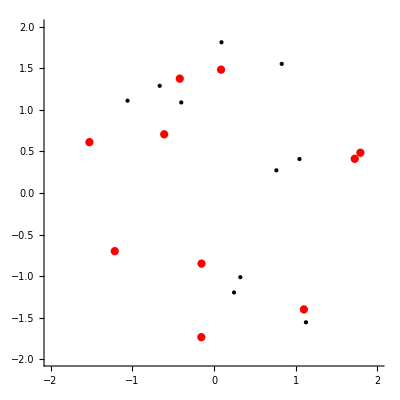

```mathematica
DrawPlasma[crap10]
```